# Homework 3

## Question 1

```mathematica
points = Solve[-x + x*y == -y/2 - x*y - x^2 == 0,{x,y}]
```

{{x→-1/2-ⅈ/2,y→1},{x→-1/2+ⅈ/2,y→1},{x→0,y→0}}

```mathematica
points[[1]]
```

{x→-1/2-ⅈ/2,y→1}

```mathematica
J[x_,y_] = {{y-1,x},{y-2x,-1/2-x}}
```

{{-1+y,x},{-2 x+y,-1/2-x}}

```mathematica
Eigensystem[J[x,y]] /. points[[1]]
```

{{1/4 (ⅈ-√(-9-24 ⅈ)),1/4 (ⅈ+√(-9-24 ⅈ))},{{(1/10-ⅈ/20) (-ⅈ-√(-9-24 ⅈ)),1},{(1/10-ⅈ/20) (-ⅈ+√(-9-24 ⅈ)),1}}}

```mathematica
Expand[(-x+x*y)^2]
```

x^2-2 x^2 y+x^2 y^2

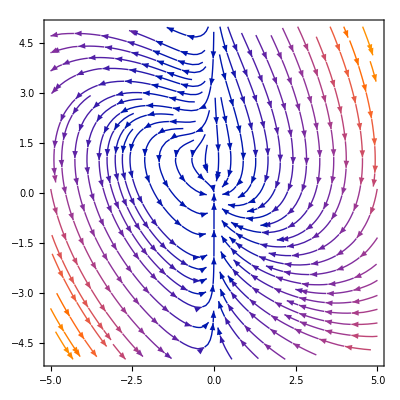

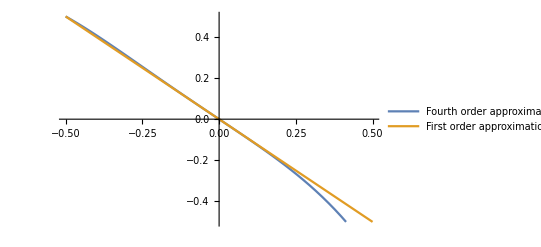

```mathematica
stream = StreamPlot[{-x + x*y,-y/2 - x*y - x^2},{x,-5,5},{y,-5,5}, Axes -> True]
plot = Plot[{-x - (2/3)*x^3 - 4/3*x^4,-x},{x,-0.5,0.5},PlotRange ->{-0.5,0.5},PlotLegends->{"Fourth order approximation","First order approximation"}]
```

```mathematica
Manipulate[Plot[m-x^2,{x,-5,5}],{m,-10,0}]
```